```mathematica
ArcCos[(4/5)]/Degree//N
```

36.8699

```mathematica
Cos[37.422Degree]
```

0.794181

```mathematica
Sqrt[2/Pi]//N
```

0.797885

```mathematica
(4/5)^2Pi//N
```

2.01062

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/adam/Dropbox/personal/projects/mathca/GRW

```mathematica
gpw15csv=Import["gpw_v4_population_count_rev11_2015_1_deg.csv"][[All,;;-2]];
gpw=Map[If[#==-9999,0.,#]&,gpw15csv,{2}];
```

```mathematica
Total[Flatten[gpw]]
```

7.32989×10^9

```mathematica
SortBy[Tally[Flatten@gpw15csv],-#[[2]]&]
```

{{-9999,45697},{0,2115},{3596.,7},{37510.1,6},{37762.2,6},{57.6472,5},{3566.86,5},{746.487,4},{751.505,4},{756.294,4},{760.853,4},{1447.07,4},{1459.45,4},{1471.37,4},{1482.85,4},{1493.88,4},{1519.17,4},16849,{1.67858×10^7,1},{1.70462×10^7,1},{1.72324×10^7,1},{1.75601×10^7,1},{1.92563×10^7,1},{2.00491×10^7,1},{2.04383×10^7,1},{2.06114×10^7,1},{2.22529×10^7,1},{2.28357×10^7,1},{2.69704×10^7,1},{2.82005×10^7,1},{2.98064×10^7,1},{3.03904×10^7,1},{3.10173×10^7,1},{3.16775×10^7,1},{3.18688×10^7,1}}
 |  |  |  |

```mathematica
Image[(#/10^6)^(1/2)&/@gpw[[;;40]]]
```

-Graphics-

```mathematica
(*gpw15clean=Map[If[Abs[#]>10^30||#==1,0,#]&,ImageData@gpw15,{2}]
gpw15trim=Map[If[Abs[#]>10^30,0,#]&,ImageData@gpw15,{2}]*)
```

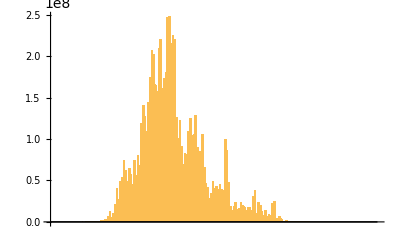

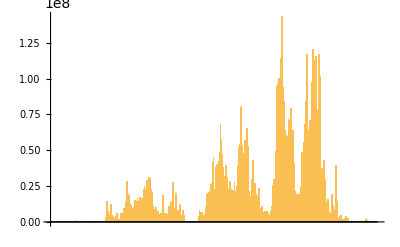

```mathematica
BarChart[Total/@gpw]
BarChart[Total/@Transpose@gpw]
```

```mathematica
Image[(Transpose[{(Mean/@gpw)}].{(Mean/@Transpose[gpw])}/10^11)]
```

-Graphics-

```mathematica
Image[gpw/10^6]
```

-Graphics-

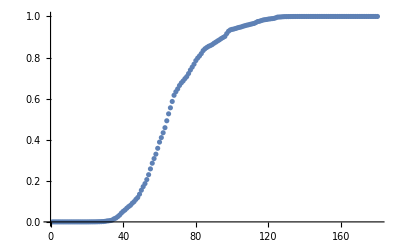

```mathematica
ListPlot[Accumulate[Total/@gpw]/Total[Flatten@gpw]]
```

```mathematica
{#,Accumulate[Total/@gpw][[#]]/Total[Flatten@gpw]}&/@Range[10,180,10]//Grid
```

10 | 8.16724×10^-8
20 | 0.0000278675
30 | 0.00266525
40 | 0.0514432
50 | 0.154141
60 | 0.388339
70 | 0.647305
80 | 0.785136
90 | 0.869592
100 | 0.937181
110 | 0.961716
120 | 0.987322
130 | 0.999332
140 | 0.999939
150 | 1.
160 | 1.
170 | 1.
180 | 1.

```mathematica
59+35
```

94

```mathematica
(Accumulate[Total/@gpw][[40]])
(Total[Flatten@gpw]-Accumulate[Total/@gpw][[-40]])
%%/Total[Flatten@gpw]
%%/Total[Flatten@gpw]
```

3.77073×10^8

400730.

0.0514432

0.0000546707

```mathematica
BarChart[Total/@Transpose@gpw]
```

-Graphics-

```mathematica
Image[gpw15clean]
```

-Graphics-